## 計算結果

```mathematica
Clear["Global`*"]
NotebookEvaluate[FileNameJoin[{NotebookDirectory[],"../../../../mathematica_utilities/mathematica_plot_options.nb"}]]
json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_multiple/result.json"
(*json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_3/result.json"*)
json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_mod_0d06/result.json"
(*json="/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_multiple_water_mod_coarse/result.json"*)
(*json="/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential/result.json"*)
imported=Import[json];
getData[var_,n_:0]:=If[n>0,(var/.imported)[[;;,n]],var/.imported];
importGetData[name_,var_,n_:0]:=With[{imported=Import[name]},If[n>0,(var/.imported)[[;;,n]],var/.imported]];
importData[name_,var_,n_:0]:=With[{imported=Import[name]},If[n>0,(var/.imported)[[;;,n]],var/.imported]];
(*Kramer20210d03=Import[NotebookDirectory[]<>"Kramer2021_0d3.csv"];*)
jsonInfo[name_]:=With[{imported=Import[name,"JSON"]},Grid[Join[{{"no.","title","length"}},Table[{i,imported[[i]][[1]],Length[imported[[i]][[2]]]},{i,1,Length[imported]}]],Frame->All,Background->{None,{LightGray,{LightGreen,Green}}}]]
jsonInfo[json]
legend=LineLegend[{"mesh A","mesh B","mesh C","mesh D","mesh E","Exp (Ren et al., 2015)"},LegendMarkerSize->20,LabelStyle->10];
plotstyle={{Red,Dashed},{Blue},{Green,Dashed},{Orange},{Magenta},{Black}};
```

plot2Doption

importData

jsonInfo

interpolateAndFourier

/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_multiple/result.json

/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_mod_0d06/result.json

no. | title | length
1 | cpu_time | 1098
2 | eq_of_motion | 1098
3 | float_COM | 1098
4 | float_EK | 1098
5 | float_EP | 1098
6 | float_accel | 1098
7 | float_area | 1098
8 | float_drag_force | 1098
9 | float_drag_torque | 1098
10 | float_force | 1098
11 | float_pitch | 1098
12 | float_roll | 1098
13 | float_torque | 1098
14 | float_velocity | 1098
15 | float_yaw | 1098
16 | gauge0_intersection | 1098
17 | gauge10_intersection | 1098
18 | gauge11_intersection | 1098
19 | gauge12_intersection | 1098
20 | gauge13_intersection | 1098
21 | gauge14_intersection | 1098
22 | gauge15_intersection | 1098
23 | gauge16_intersection | 1098
24 | gauge17_intersection | 1098
25 | gauge18_intersection | 1098
26 | gauge19_intersection | 1098
27 | gauge1_intersection | 1098
28 | gauge2_intersection | 1098
29 | gauge3_intersection | 1098
30 | gauge4_intersection | 1098
31 | gauge5_intersection | 1098
32 | gauge6_intersection | 1098
33 | gauge7_intersection | 1098
34 | gauge8_intersection | 1098
35 | gauge9_intersection | 1098
36 | simulation_time | 1098
37 | wall_clock_time | 1098
38 | water_E | 1098
39 | water_EK | 1098
40 | water_EP | 1098
41 | water_face_size | 1098
42 | water_point_size | 1098
43 | water_volume | 1098

```mathematica
(*i=1;
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importGetData[json,name,1]-importGetData[json,name,1][[1]]],{i,1,20,1}]
,Joined->True
]
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importGetData[json,name,2]-importGetData[json,name,2][[1]]],{i,1,20,1}]
,Joined->True
]
ListPlot[
Table[With[{name="float"<>ToString[i]<>"_COM"},importGetData[json,name,3]-importGetData[json,name,3][[1]]],{i,1,20,1}]
,Joined->True
]*)
```

```mathematica
(*Tshift=6.5*)
Tshift=-7.55

ExpHeave={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_heave_exp.csv"];
SimuHeave={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_heave_simu.csv"];
ExpSway={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_sway_exp.csv"];
SimuSway={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_sway_simu.csv"];
ExpRoll={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_roll_exp.csv"];
SimuRoll={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_roll_simu.csv"];
ExpSf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Sf_exp.csv"];
SimuSf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Sf_simu.csv"];
SimuRm={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Rm_simu.csv"];
SimuHf={#1-Tshift,#2}&@@@Import["/Users/tomoaki/Library/CloudStorage/Dropbox/code/cpp/builds/build_bem/study_benchmark/Tanizawa1996/lambda1d8m_H0d05m_Hf_simu.csv"];
```

-7.55

```mathematica
ζa=0.05/2;
{B,L}={0.74,0.997};(*{Bredth,Length}*)
g=9.8;
ρ=1000;
λ=1.8;
ρgLBζa=ρ*g*L*B*ζa

h=4.5;
Omega[k_,h_]:=Sqrt[g*k*Tanh[h*k]];
Tw=T/.Solve[Omega[2π/λ,h]==2π/T,T][[1]];
```

180.756

Solve::ratnz: Solveは厳密でない係数の系を解くことができませんでした．解は対応する厳密系を解き，結果を数値に変換することで得られました．

## 計算結果

```mathematica
fourColorScheme={
{Thick,Blue(*RGBColor[55/255,126/255,184/255]*)},
{Thickness[0.002],Red(*RGBColor[255/255,127/255,0]*)},
{Thickness[0.002],RGBColor[77/255,175/255,74/255]},
{Thickness[0.002],RGBColor[247/255,129/255,191/255]}};
threeColorScheme={{Thick,RGBColor[55/255,126/255,184/255]},RGBColor[255/255,127/255,0],RGBColor[77/255,175/255,74/255]};
plotxrange={{5,30},All};
opt={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
Epilog->{Line[{{-100,0},{100,0}}]},
Joined->{True,True,True,False},
PlotRange->plotxrange,
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->1000,
(*PlotStyle->{{Blue},{Red},{Darker[Green]}},*)
PlotStyle->fourColorScheme,
AspectRatio->1/8};
(*メッシュと計算の収束*)
```

```mathematica
simutime=importGetData[json,"simulation_time"]/Tw;
```

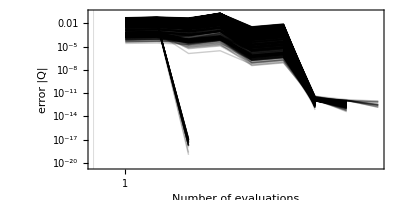

```mathematica
(*データのインポート*)
data=importData[json,"eq_of_motion"];
data=data[[(*Round[Length[data]/10]*);;(*Round[2Length[data]/10]*)]];
(*データセットの数に基づいてグレースケールの濃さを計算*)
numDataSets=Length[data];
grayLevels=Table[GrayLevel[i/(numDataSets-1)],{i,0,numDataSets-1}];

(*プロット*)
ListLogPlot[Transpose[{Range[Length[#]],#}]&@@@data,
(*PlotRange->{{1,10},All},*)
PlotRange->Automatic,
PlotStyle->Directive[Thin,Black,Opacity[0.2]],
FrameTicks->{{All,Automatic},{Table[i,{i,1,100,5}],None}},
AspectRatio->1/2,
FrameLabel->{
Style["Number of evaluations",FontSize->20,FontFamily->"Times"],
Rotate[Style["error |Q|",FontSize->20,FontFamily->"Times"],-π/2]},
Frame->True,
Evaluate[plot2Doption]
]
```

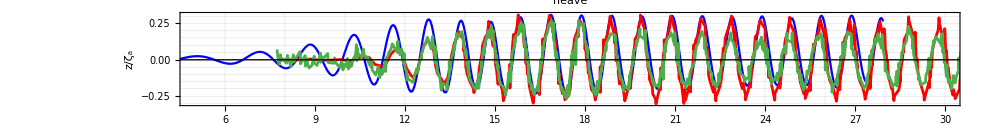

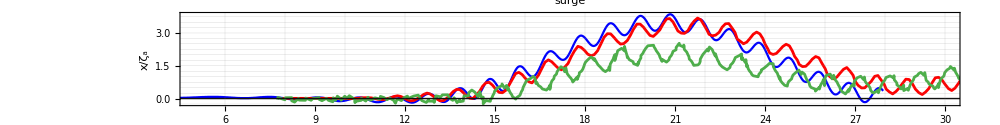

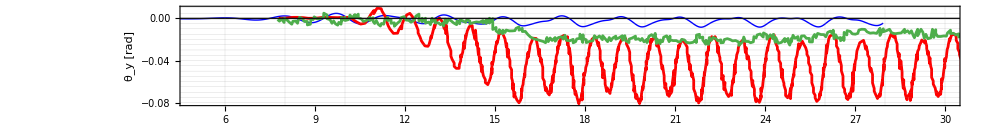

```mathematica
fig=ListPlot[
{{simutime,(importGetData[json,"float_COM",3]-importGetData[json,"float_COM",3][[1]])/ζa}ᵀ,
SimuHeave,
ExpHeave
},
Evaluate[opt],
PlotStyle->plotstyle,
(*PlotRange->{{0,12.},{-0.07,0.07}},*)
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z/ζ_a",FontSize->20,FontFamily->"Times"]},
PlotLegends->legend,
PlotLabel->"heave",
Evaluate[plot2Doption]
]
ListPlot[
{{simutime,(importGetData[json,"float_COM",1]-importGetData[json,"float_COM",1][[1]])/ζa}ᵀ,
SimuSway,
ExpSway
},
Evaluate[opt],
PlotStyle->plotstyle,
PlotRange->{All,Automatic},
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/ζ_a",FontSize->20,FontFamily->"Times"]},
PlotLegends->legend,
PlotLabel->"surge",
Evaluate[plot2Doption]
]

k=2π/λ;
ListPlot[
{{simutime,-(importGetData[json,"float_pitch"])}ᵀ,
SimuRoll,
ExpRoll
},
Evaluate[opt],
PlotStyle->plotstyle,
PlotRange->{All,All},
PlotRange->{Automatic,Automatic},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["θ_y [rad]",FontSize->20,FontFamily->"Times"]},
Evaluate[plot2Doption]
]
```

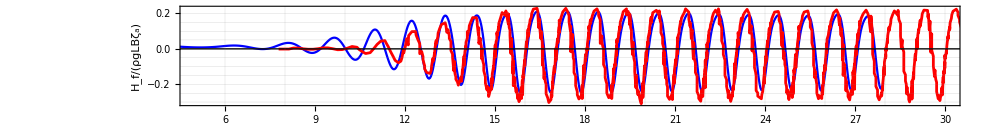

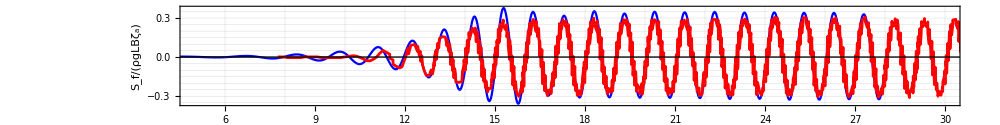

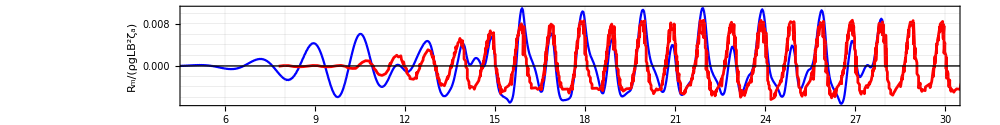

```mathematica
ListPlot[
Append[Table[{simutime,((importGetData[json,"float_force",i]-importGetData[json,"float_force",i][[5]])/(ρ*g*L*B*ζa))}ᵀ,{i,3,3,1}],
SimuHf],
Evaluate[opt],
PlotStyle->plotstyle,
PlotRange->{All,All},
PlotRange->{Automatic,Automatic},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["H_f/(ρgLBζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]

ListPlot[
Append[Table[{simutime,((importGetData[json,"float_force",i]-importGetData[json,"float_force",i][[5]])/(ρ*g*L*B*ζa))}ᵀ,{i,1,1,1}],
SimuSf],
Evaluate[opt],
PlotStyle->plotstyle,
PlotRange->{All,All},
PlotRange->{Automatic,Automatic},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["S_f/(ρgLBζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]

ListPlot[
Append[Table[{simutime,-((importGetData[json,"float_torque",i]-importGetData[json,"float_torque",i][[15]])/(ρ*g*L*B*B*ζa))}ᵀ,{i,2,2,1}],
SimuRm],
Evaluate[opt],
PlotStyle->plotstyle,
PlotRange->{All,All},
PlotRange->{Automatic,Automatic},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["R_m/(ρgLB^2ζ_a)",FontSize->20,FontFamily->"Times"]},
PlotLegends->{"x","y","z"},
Evaluate[plot2Doption]
]
```

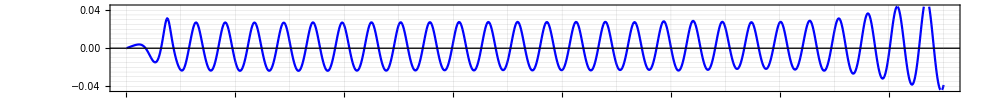
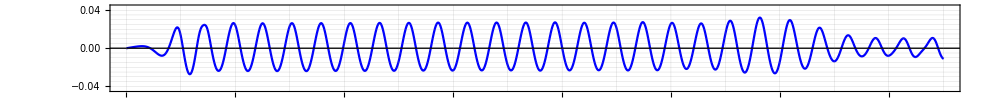
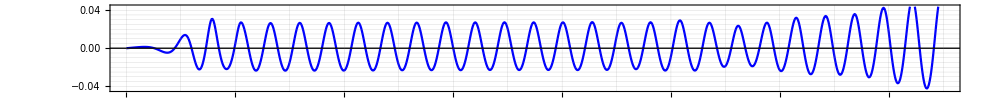
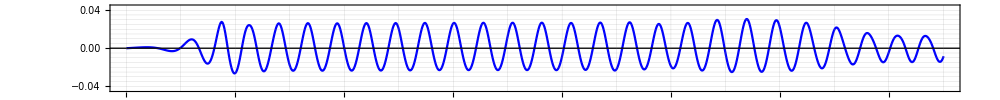
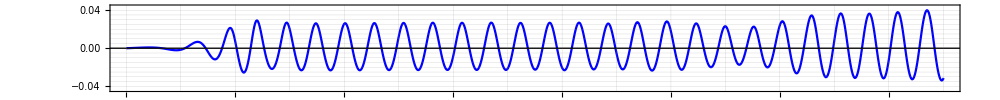
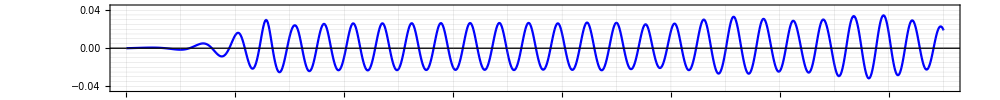
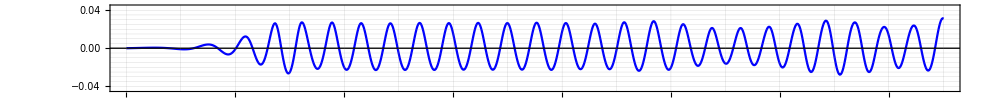
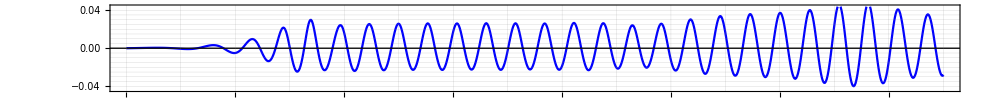
-Graphics-0.7
-Graphics-1.2
-Graphics-1.7
-Graphics-2.2
-Graphics-2.7
-Graphics-3.2
-Graphics-3.7
-Graphics-4.2
-Graphics-4.7
-Graphics-5.2
-Graphics-5.7
-Graphics-6.2
-Graphics-6.7
-Graphics-7.2
-Graphics-7.7
-Graphics-8.2
-Graphics-8.7
-Graphics-9.2
-Graphics-9.7

```mathematica
Column[Table[
With[{DATA=importGetData[json,data,3]},
Labeled[
ListPlot[
{importGetData[json,"simulation_time"],(DATA-DATA[[1]])}ᵀ,
(*FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x/H_0",FontSize->20,FontFamily->"Times",Italic]},*)
AspectRatio->1/10,
PlotRange->{Automatic,1.75*{-ζa,ζa}},
Joined->{True,True,True,True,True},
Evaluate[opt],
PlotStyle->plotstyle,
(*Mesh->All,*)
(*PlotRange->{All,All},*)
Evaluate[plot2Doption]
]
,importGetData[json,data,1][[1]]
,Right]
],
{data,Table["gauge"<>ToString[i]<>"_intersection",{i,1,19,1}]}]
,Spacings->0
]
```

## 収束性のチェック

```mathematica
plotstyle=Table[RGBColor[{Sin[i*π]/2+1/2,Cos[i*π]/2+1/2,i}],{i,0,1,0.2}]
legend={(*"0.1",*)"0.09","0.08","0.07","0.06"}
```

{RGBColor[{0.5, 1., 0.}],RGBColor[{0.7938926261462366, 0.9045084971874737, 0.2}],RGBColor[{0.9755282581475768, 0.6545084971874737, 0.4}],RGBColor[{0.9755282581475768, 0.3454915028125262, 0.6000000000000001}],RGBColor[{0.7938926261462367, 0.09549150281252633, 0.8}],RGBColor[{0.5000000000000001, 0., 1.}]}

{0.09,0.08,0.07,0.06}

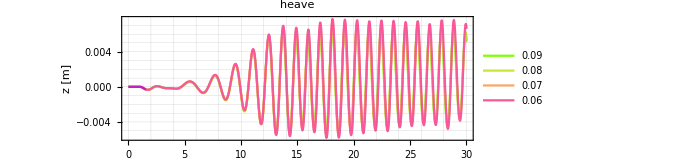

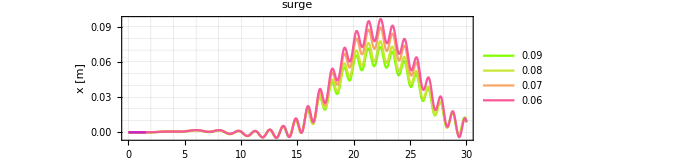

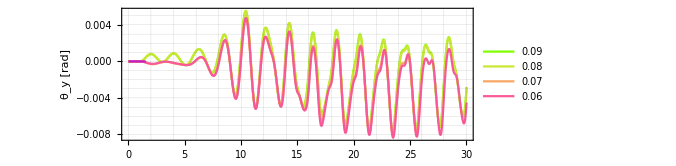

```mathematica
jsons={(*"/Volumes/home/BEM/20240301土木学会東北支部/Tanizawa1996_H0d05_L1d8_potential_water_mod_0d1/result.json",*)
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_mod_0d09/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_mod_0d08/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_mod_0d07/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_mod_0d06/result.json",
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_water_mod_0d05/result.json"(*,
"/Users/tomoaki/BEM/Tanizawa1996_H0d05_L1d8_potential_3/result.json"*)};

plotxrange={{0,30},All};
opt={FrameStyle->Directive[FontSize->16,Black,Thickness[0.002]],
PlotStyle->plotstyle,
Joined->{True,True,True,True},
PlotRange->plotxrange,
GridLines->All,
GridLinesStyle->Directive[Gray,AbsoluteThickness[0.001]],
ImageSize->500,
(*PlotStyle->{{Darker[Blue,0.1]},{Darker[Blue,0.3]},{Darker[Blue,0.6]},{Darker[Blue,0.9]}},*)
AspectRatio->1/3};
(*メッシュと計算の収束*)

fig=ListPlot[
Table[{importGetData[jsons[[i]],"simulation_time"],(importGetData[jsons[[i]],"float_COM",3]-Mean@importGetData[jsons[[i]],"float_COM",3][[1;;10]])}ᵀ,
{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt],
(*PlotRange->{{0,12.},{-0.07,0.07}},*)
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["z [m]",FontSize->20,FontFamily->"Times"]},
PlotLegends->legend,
PlotLabel->"heave",
Evaluate[plot2Doption]
]
ListPlot[
Table[{importGetData[jsons[[i]],"simulation_time"],(importGetData[jsons[[i]],"float_COM",1]-Mean@importGetData[jsons[[i]],"float_COM",1][[1;;10]])}ᵀ,{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt],
PlotRange->{All,Automatic},
GridLines->{Table[i,{i,0.,6.,0.2}],Table[i,{i,-1.,1.,0.5}]},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["x [m]",FontSize->20,FontFamily->"Times"]},
PlotLegends->legend,
PlotLabel->"surge",
Evaluate[plot2Doption]
]
k=2π/λ;
ListPlot[
Table[{importGetData[jsons[[i]],"simulation_time"],-(importGetData[jsons[[i]],"float_pitch"]-importGetData[jsons[[i]],"float_pitch"][[1]])}ᵀ,{i,1,Length[jsons]}],
PlotStyle->plotstyle,
Evaluate[opt],
PlotLegends->legend,
PlotRange->{All,All},
PlotRange->{Automatic,Automatic},
FrameLabel->{Style["t/T",FontSize->20,FontFamily->"Times",Italic],Style["θ_y [rad]",FontSize->20,FontFamily->"Times"]},
Evaluate[plot2Doption]
]
```